```mathematica
(*Function which takes a 'corner' of a hexagon (or triangle) and produces all the weights in the triangle
All weights are in the basis of the fundamental dominant weights
The roots are in the basis of the simple roots *)
ShellWeights[dominantweight_]:=Module[{weights,nextweight},
(*Gets edge in alpha direction (top of hexagon)*)
weights=Join[{dominantweight},Edge[dominantweight,{1,0}]];
nextweight=Last[weights];
(*Gets edge in alpha+beta direction, etc.*)
weights=Join[weights,Edge[nextweight,{1,1}]];
nextweight=Last[weights];
weights=Join[weights,Edge[nextweight,{0,1}]];
nextweight=Last[weights];
weights=Join[weights,Edge[nextweight,{1,0}]];
nextweight=Last[weights];
weights=Join[weights,Edge[nextweight,{1,1}]];
nextweight=Last[weights];
weights=Join[weights,Edge[nextweight,{0,1}]];
(*weights=Delete[weights,Length[weights]]*)
Return[weights];
];
(*Takes extremal weight of sl_2 module corresponding to root, gets all weights from that rep*)
Edge[weight_,root_]:=Module[{n,cartanmatrix},
n=Dot[weight,root];
(*Used to change basis from simple roots to fundamental dominant weight*)
cartanmatrix={{2,-1},{-1,2}};
If[n<0,Table[weight+x*(cartanmatrix.root),{x,1,-n}],Table[weight-x*(cartanmatrix.root),{x,1,n}]]];
(*Plots a given collection of weights in Euclidean coordinates*)
PlotWeights[weights_]:=Module[{cobmatrix},
cobmatrix={{Sqrt[3]/2,0},{1/2,1}};
ListPlot[Transpose[cobmatrix.Transpose[weights]]]]
```

```mathematica
(*Examples*)
(*Defining Rep*)
ShellWeights[{1,0}]
```

{{1,0},{-1,1},{0,-1},{1,0}}

```mathematica
(*Ad Rep Outer Shell*)
ShellWeights[{1,1}]
```

{{1,1},{-1,2},{-2,1},{-1,-1},{1,-2},{2,-1},{1,1}}

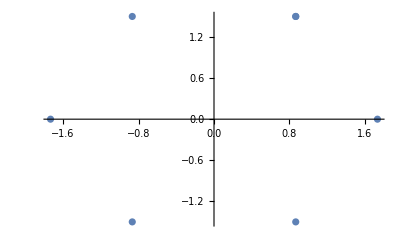

```mathematica
PlotWeights[ShellWeights[{1,1}]]
```

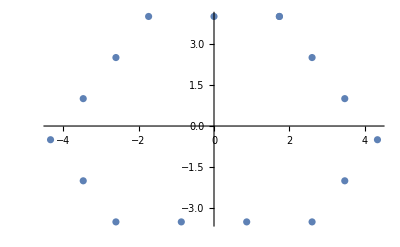

```mathematica
PlotWeights[ShellWeights[{2,3}]]
```